# 复杂直线区域绘图问题

把代码都写到一起是坏习惯。要合理分单元，方便调试。

## 问题

n=5 时就画不出来了。分单元运行发现，不是 While 循环卡死，而是卡在画图这一步：

```mathematica
j=1;
a=ImplicitRegion[x^2+y^2≤1&&y≥x+38,{x,y}];
n=5;
```

```mathematica
While[j≤n,
i=0;While[i≤j,
d=ImplicitRegion[y≥j*(x-i/j),{x,y}];
e=ImplicitRegion[y≥-j*(x-i/j),{x,y}];
c=RegionIntersection[d,e];
a=RegionUnion[a,c];i++];
j++];
```

这么直接画就画不了了……

```mathematica
TimeConstrained[
RegionPlot[a,Axes->True,Frame->True,PlotRange->{{0,1},{0,1}}]
,10]
```

$Aborted

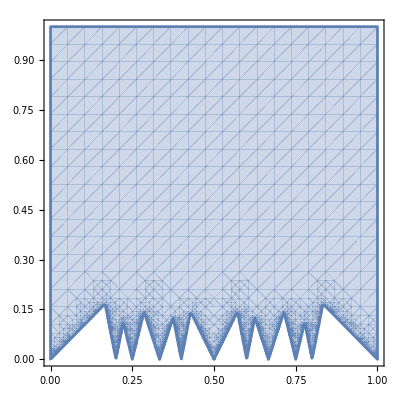

```mathematica
TimeConstrained[
RegionPlot[Evaluate@a[[1]],{x,0,1},{y,0,1},Axes->True,Frame->True,PlotRange->{{0,1},{0,1}},MaxRecursion->8]
,10]
```

Region 能画但调不了精度

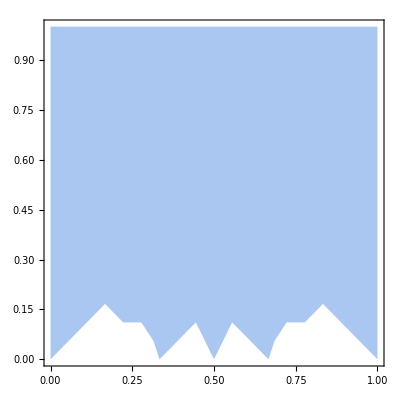

```mathematica
TimeConstrained[
Region[a,Axes->True,Frame->True,PlotRange->{{0,1},{0,1}}]
,10]
```

## 观察

n =2 时能画出来

```mathematica
j=1;
a=ImplicitRegion[x^2+y^2≤1&&y≥x+38,{x,y}];
n=2;
```

```mathematica
While[j≤n,
i=0;While[i≤j,
d=ImplicitRegion[y≥j*(x-i/j),{x,y}];
e=ImplicitRegion[y≥-j*(x-i/j),{x,y}];
c=RegionIntersection[d,e];
a=RegionUnion[a,c];i++];
j++];
```

```mathematica
RegionPlot[a,Axes->True,Frame->True,PlotRange->{{0,1},{0,1}}]
```

-Graphics-

用 Mesh->All 可以看到它自适应网格细化是怎么做的

```mathematica
RegionPlot[a,Axes->True,Frame->True,PlotRange->{{0,1},{0,1}},Mesh->All]
```

-Graphics-

注意到文档里 RegionPlot 的语法其实不是用来直接放入一个 Region 的，而是放入 Region 的判定条件 pred，我们尝试用区域对应的判定条件：

```mathematica
a
a[[1]]
```

ImplicitRegion[(y≥x&&x+y≥0)||(1+y≥x&&x+y≥1)||(y≥2 x&&y≥-2 x)||(1+y≥2 x&&2 x+y≥1)||(2+y≥2 x&&2 x+y≥2),{x,y}]

(y≥x&&x+y≥0)||(1+y≥x&&x+y≥1)||(y≥2 x&&y≥-2 x)||(1+y≥2 x&&2 x+y≥1)||(2+y≥2 x&&2 x+y≥2)

```mathematica
a[[1,5]]
```

2+y≥2 x&&2 x+y≥2

奇怪的是，这个条件组合居然画出来很不对！即便增大递归细分数也不行 MaxRecursion->6
观察发现，本来不该是边缘的地方它却当作边界进行细分了。不知道为什么，可能是采样时候符号处理的问题

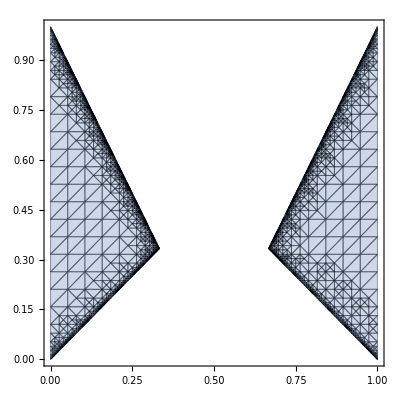

```mathematica
RegionPlot[a[[1]],{x,0,1},{y,0,1},Axes->True,Frame->True,PlotRange->{{0,1},{0,1}},Mesh->All,MaxRecursion->6]
```

## 解决

既然如此，尝试用判定条件的语法，但把条件 pred 搞成黑箱 or 在画图之前展开。几种方法都有效。直接看结果吧：
比较下来，后者 a[[1]]//Evaluate 比较有效，比较快。绘图精度可以通过 MaxRecursion->6 修改

```mathematica
j=1;
a=ImplicitRegion[x^2+y^2≤1&&y≥x+38,{x,y}];
n=5;
```

```mathematica
While[j≤n,
i=0;While[i≤j,
d=ImplicitRegion[y≥j*(x-i/j),{x,y}];
e=ImplicitRegion[y≥-j*(x-i/j),{x,y}];
c=RegionIntersection[d,e];
a=RegionUnion[a,c];i++];
j++];
```

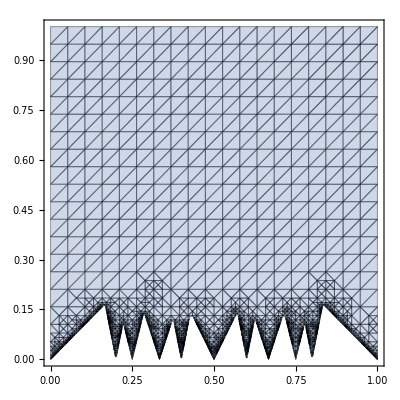

```mathematica
regmem=RegionMember[a];
RegionPlot[regmem@{x,y},{x,0,1},{y,0,1},Axes->True,Frame->True,PlotRange->Full,MaxRecursion->6,Mesh->All]
```

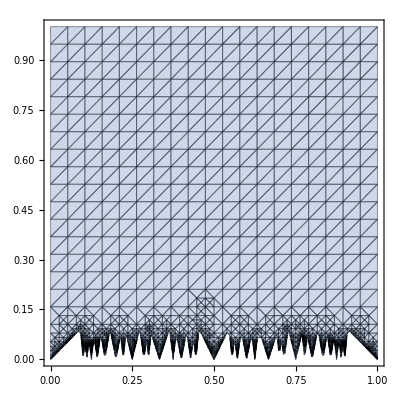

```mathematica
RegionPlot[a[[1]]//Evaluate,{x,0,1},{y,0,1},Axes->True,Frame->True,PlotRange->Full,MaxRecursion->6,Mesh->All]
```